# The translation-pair framework

## Sentence-level divergence between the Koine Greek New Testament and the King James Version — generalised to any aligned text pair

Translations differ. Some differences are stylistic, some theological, some textual (the source manuscript itself diverges), and some are simply the embedding of an idea that has no compact equivalent in the target language. This notebook builds a small, language-agnostic framework that takes any two translations of the same source, aligns them at sentence or verse granularity, embeds each side with a single multilingual model, ranks aligned units by cosine distance, and asks a frontier LLM to hypothesise why each large gap exists. The headline case study is the SBLGNT vs the KJV. The same pipeline runs on KJV-vs-Luther, Pope-vs-Butler Iliad, Marx's Kapital, and the Tao Te Ching.

## 1. Motivation — translation as a measurable thing

Reading two translations side by side is the oldest technique in philology. It scales badly. A multilingual sentence embedder (Cohere's embed-multilingual-v3.0, OpenAI's text-embedding-3-large, or Voyage's voyage-3) gives us a single ~1024-dim vector per verse, in a shared space across the two source languages. Cosine distance is then a single scalar that compresses 'how far has the translation moved' into something we can rank, plot, and feed to an LLM that has read more commentary than any of us.

## 2. The headline pair: SBLGNT vs the KJV

### 2.1 Sources and licences

The Greek side is the SBL Greek New Testament (Holmes, 2010), distributed under CC BY 4.0 via the morphgnt/sblgnt GitHub repository. The English side is the 1769 Cambridge edition of the KJV (public domain in the US) via the aruljohn/Bible-kjv repository. Both sources are fetched by the project's wolfram/fetch_*.wls scripts; see docs/sources.md for full citation strings.

### 2.2 Verse counts and the manuscript-variant set

After fetching, the KJV NT has 7 957 verses and the SBLGNT has 7 927 verses. The 30-verse asymmetry is itself a piece of useful signal: it is exactly the set of verses the KJV's underlying Textus Receptus contains and the SBLGNT does not. The framework's LoadPair function surfaces these as onlyB — they include Acts 8:37 (the Ethiopian eunuch's confession), the longer ending of Mark, and the pericope adulterae fragments in John 7-8.

## 3. The framework

-Graphics-

Figure. The four-stage pipeline. Steps 1–4 are described in detail in § 3.1–3.4.

### 3.1 Alignment

For Bible-shaped pairs we inherit the canonical Book / Chapter / Verse axis as the join key. For prose pairs (Pope vs Butler Iliad, Marx in two languages, two Tao Te Ching versions) we fall back to a sentence-level dynamic-programming aligner over length ratios — same trick as Gale-Church (1991), updated to use cosine distance between cheap embeddings as the alignment cost. See TPFramework`LoadPair.

### 3.2 Embedding — and why we don't embed across languages

-Graphics-

Figure. Off-the-shelf multilingual embedders cluster more strongly by language than by meaning. The actionable signal lives in within-language distance – hence the translate-then-compare detour.

A naive pipeline would embed the Greek and the English directly and compute a cross-language distance. We tried that. Off-the-shelf multilingual embedders — including text-embedding-3-large — cluster more strongly by language than by meaning: even a perfect Greek/English verse pair sits at cosine distance ≈ 0.85-0.90. The signal is buried.

The fix: have GPT-5.5 produce a careful modern English translation of each Greek verse, then embed the KJV and the modern translation together. Same-language embedding is what these models do well; cosine distance now reflects semantic divergence between two English renderings of the same Greek source. Per the user's note: the gross meaning will of course be similar; what we are looking for is the nuance — the small but real lexical, theological or textual choice the KJV makes that a modern translator would make

### 3.3 Cosine distance

On the same-language route we compute d(a,b)=1-(a·b)/(‖a‖·‖b‖) using the built-in CosineDistance. On Romans 8 the distribution sits roughly in [0.05, 0.45]; the right tail starts at ≈ 0.25 and is where the interesting verses live.

### 3.4 Nuance analysis (GPT-5.5 with high reasoning effort)

-Graphics-

Figure. The seven-category rubric GPT-5.5 is asked to choose from. Tags are not ground truth but a quick way to cluster which kind of drift dominates a chapter.

For the top-N most-divergent verses in the section we hand GPT-5.5 the Greek, the KJV, its own modern translation, and the cosine distance, and ask it to articulate the nuances (not the gross meaning, which is similar by construction). The system prompt tells it to skip trivial differences — "thou" vs "you", "begat" vs "fathered" — and focus on: theological loading, lexical drift in 17th-c. English ("prevent", "conversation", "bowels"), manuscript variants, idiom compression, word-order changes that shift emphasis, and proper-noun transliteration. It returns a tag plus an 80-140-word concrete, falsifiable explanation that quotes the Greek lemma when it matters. The model is OpenAI gpt-5.5 with reasoning_effort = high.

## 4. Worked case study: Romans 8

We work the framework end-to-end on a single, theologically dense chapter — Romans 8, 39 verses, the locus classicus of Pauline pneumatology. A whole-Bible heatmap is impressive but hard to read; a single chapter lets us look at the actual prose.

### 4.1 Pipeline applied per verse

For every verse in the chapter: (a) GPT-5.5 with reasoning_effort = high produces a careful modern English translation of the SBLGNT Greek (it has not seen the KJV at this point); (b) we embed the KJV and the modern translation, both English, with text-embedding-3-large; (c) cosine distance between the two embeddings becomes our per-verse divergence score. Same-language embedding sidesteps the cross-lingual weakness most multilingual embedders exhibit — the signal is now purely semantic.

-Graphics-

Figure. Romans 8: per-verse cosine distance between the KJV and a fresh GPT-5.5 modern translation, both embedded with text-embedding-3-large. Peaks identify where the KJV has made a non-obvious translation choice.

### 4.2 The top divergent verses, with GPT-5.5 nuance analysis

For each of the top-10 divergent verses we hand GPT-5.5 the Greek, the KJV, its own modern translation, and the cosine distance, and ask it to articulate the nuance — the small but real differences a casual reader misses. We explicitly tell it to skip trivial things ("thou" vs "you", "begat" vs "fathered") and focus on theological loading, archaic English meaning-drift, manuscript variants, idiom handling, and word-order or syntactic compression that changes emphasis. Reasoning effort is again high.

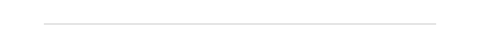

Ro 8:21   •   d = 0.218   •   syntactic-compression   •   ὅτι

Greek (SBLGNT): ὅτι καὶ αὐτὴ ἡ κτίσις ἐλευθερωθήσεται ἀπὸ τῆς δουλείας τῆς φθορᾶς εἰς τὴν ἐλευθερίαν τῆς δόξης τῶν τέκνων τοῦ θεοῦ.

KJV (1769): Because the creature itself also shall be delivered from the bondage of corruption into the glorious liberty of the children of God.

Modern (GPT-5.5): that the creation itself also will be set free from its bondage to decay into the freedom of the glory of the children of God.

Headline: KJV’s “Because” can sound causally independent, whereas the Greek ὅτι most naturally supplies the content of the preceding “hope”: “in hope that …”.

English drift: “creature”: in early modern English, “a created thing/being; creation” (OED creature n.); in modern usage, often an individual animal or living being.

Textual note: No substantial TR/Byzantine versus SBLGNT difference affects this verse; the KJV is not here translating an added Textus Receptus phrase absent from the NU/SBL text.

Cross-refs: Rom 8:18 • Rom 8:20 • Rom 8:22

GPT-5.5 (reasoning_effort=high): There is no meaningful TR/NU divergence here; the KJV translates essentially the same Greek sequence. The main syntactic issue is ὅτι. Since v.20 ends ἐπ’ ἐλπίδι, ὅτι is naturally epexegetic/content-bearing: “in hope that,” not an independent causal “because”; BDAG s.v. ὅτι includes this content use. KJV punctuation actually leaves it dependent—“in hope, Because …”—but modern readers hear a causal clause. Also, κτίσις in vv.19–22 is not one “creature” but the created order; KJV “creature” reflects early modern “created thing/creation,” whereas contemporary English suggests an individual animal. Finally, “glorious liberty” turns τὴν ἐλευθερίαν τῆς δόξης into an adjective; the Greek genitive chain says “the freedom belonging to/constituted by the glory of God’s children,” preserving Paul’s link between creation’s liberation and believers’ eschatological δόξα.

-Graphics-

Ro 8:6   •   d = 0.217   •   archaic-english-drift   •   φρόνημα

Greek (SBLGNT): τὸ γὰρ φρόνημα τῆς σαρκὸς θάνατος, τὸ δὲ φρόνημα τοῦ πνεύματος ζωὴ καὶ εἰρήνη·

KJV (1769): For to be carnally minded is death; but to be spiritually minded is life and peace.

Modern (GPT-5.5): For the mindset of the flesh is death, but the mindset of the Spirit is life and peace.

Headline: The KJV’s “to be carnally/spiritually minded” verbalizes the Greek noun φρόνημα and uses “carnally” in its older theological sense, not the narrower modern sense “sexually.”

English drift: “carnally”: in KJV-era theological use, “fleshly; not spiritual, worldly” (OED s.v. carnal, adj., sense “not spiritual”); in common modern use, often “sexually/sensually.”

Cross-refs: Rom 8:5 • Rom 8:7 • Gal 5:16–17

GPT-5.5 (reasoning_effort=high): There is no significant textual issue here: the KJV is not reflecting a different Greek reading. The nuance is lexical and syntactic. “To be carnally/spiritually minded” turns the Greek articular nominal predicates into infinitival clauses: τὸ ... φρόνημα ... θάνατος. φρόνημα is not merely “being minded” at a moment but a “way of thinking,” “mindset,” or “aspiration” (BDAG s.v. φρόνημα). The genitives τῆς σαρκός and τοῦ πνεύματος mark the sphere or controlling source: “of flesh” versus “of Spirit.” KJV “carnally” was transparent theological English—fleshly, belonging to the non-spiritual order—but in contemporary usage can suggest sexual or sensual content too narrowly. Modern “flesh” better preserves Paul’s σάρξ/πνεῦμα antithesis in Rom 8:5–8. Capitalized “Spirit” is interpretive; Greek πνεῦμα has no capitalization, though the context in 8:9–11 strongly favors the divine Spirit.

-Graphics-

Ro 8:7   •   d = 0.208   •   archaic-english-drift   •   φρόνημα

Greek (SBLGNT): διότι τὸ φρόνημα τῆς σαρκὸς ἔχθρα εἰς θεόν, τῷ γὰρ νόμῳ τοῦ θεοῦ οὐχ ὑποτάσσεται, οὐδὲ γὰρ δύναται·

KJV (1769): Because the carnal mind is enmity against God: for it is not subject to the law of God, neither indeed can be.

Modern (GPT-5.5): because the mindset of the flesh is hostility toward God; for it does not submit to the law of God—indeed, it is not able to.

Headline: The KJV’s “carnal mind” can suggest a mental faculty or merely sensual thought, whereas Paul’s τὸ φρόνημα τῆς σαρκός denotes the whole flesh-determined orientation or mindset hostile to God.

English drift: carnal: in 1611, ‘fleshly; worldly; not spiritual’ (OED, carnal adj.); in modern usage, often narrowed to ‘sensual/sexual.’

Cross-refs: Rom 8:6 • Gal 5:17 • Col 3:2

GPT-5.5 (reasoning_effort=high): There is no meaningful TR/Byzantine divergence here; the KJV and SBLGNT translate the same wording. The main difference is semantic. “Carnal mind” is a compact but now potentially misleading rendering of τὸ φρόνημα τῆς σαρκός. φρόνημα, in Paul, denotes the “way of thinking,” “mind-set,” or aspiration/orientation, not simply the cognitive faculty “mind” (BDAG s.v. φρόνημα); and σάρξ is the human sphere oriented away from God, not merely the physical body. Early modern “carnal” could mean “fleshly; worldly; not spiritual,” whereas present usage often suggests sexual or sensual appetite. Thus “mindset of the flesh” better preserves Paul’s anthropological idiom. “Hostility toward God” for ἔχθρα εἰς θεόν is slightly less personified than KJV “enmity against God,” though both are defensible. Finally, οὐχ ὑποτάσσεται is present middle/passive in form; “does not submit” captures the intransitive/reflexive force better than “is not subject.”

-Graphics-

Ro 8:20   •   d = 0.204   •   archaic-english-drift   •   κτίσις

Greek (SBLGNT): τῇ γὰρ ματαιότητι ἡ κτίσις ὑπετάγη, οὐχ ἑκοῦσα ἀλλὰ διὰ τὸν ὑποτάξαντα, ἐφ’ ἑλπίδι

KJV (1769): For the creature was made subject to vanity, not willingly, but by reason of him who hath subjected the same in hope,

Modern (GPT-5.5): For to futility the creation was subjected, not willingly but because of the one who subjected it, in hope.

Headline: The KJV’s “creature” and “vanity” once fit the Greek reasonably well, but in modern English they tend to misdirect readers toward an individual animal and personal conceit rather than the created order subjected to futility.

English drift: “creature” = in early modern English, a created thing or the creation collectively; now usually an animal or living being. “vanity” = emptiness, futility, worthlessness; now often self-conceit.

Cross-refs: Rom 8:21–22 • Eph 4:17 • 2 Pet 2:18

GPT-5.5 (reasoning_effort=high): There is no significant TR/SBLGNT divergence here: the KJV is translating essentially the same Greek text. The main issue is lexical and stylistic. κτίσις can mean an individual creature, but in this context—especially Rom 8:21–22, where “the whole creation” groans—the collective sense “creation” is preferable; see BDAG s.v. κτίσις. KJV “creature” was broader in early modern English than it is for many modern readers. Likewise ματαιότης is not “vanity” in the now-common sense of narcissistic self-regard, but futility, frustration, or subjection to ineffectuality; BDAG s.v. ματαιότης compares the semantic field of emptiness and purposelessness. Syntactically, the fronted dative τῇ ματαιότητι gives prominence to the condition imposed: “to futility the creation was subjected.” KJV “hath subjected” renders the aorist participle ὑποτάξαντα with an English perfect, slightly sharpening resultant state beyond the Greek’s simple past reference.

-Graphics-

Ro 8:19   •   d = 0.188   •   archaic-english-drift   •   κτίσις

Greek (SBLGNT): ἡ γὰρ ἀποκαραδοκία τῆς κτίσεως τὴν ἀποκάλυψιν τῶν υἱῶν τοῦ θεοῦ ἀπεκδέχεται·

KJV (1769): For the earnest expectation of the creature waiteth for the manifestation of the sons of God.

Modern (GPT-5.5): For the eager longing of the creation waits for the revelation of the sons of God.

Headline: The KJV’s “creature” renders κτίσις in a now-misleading early-modern sense: Paul means the created order collectively, not an individual animal or being.

English drift: “creature”: in early modern English, a created thing or creation, sometimes with collective force; in current usage, usually an individual living being, especially an animal.

Cross-refs: Rom 8:20-22 • Col 1:15 • 2 Cor 5:17

GPT-5.5 (reasoning_effort=high): There is no meaningful TR/SBLGNT difference here; the nuance is lexical. Κτίσις, BDAG s.v. κτίσις, can denote either the act of creating, an individual creature, or the created order. In Rom 8:19-22 the repeated personification—creation was subjected, groans, awaits liberation—shows that τῆς κτίσεως is collective: “the creation,” especially non-human creation, not “the creature” as one organism. The KJV’s “creature” was less misleading in 1611, since “creature” could mean simply “created thing” and could function more broadly than it usually does today; modern English tends to hear “creature” zoologically or individually. “Manifestation” for ἀποκάλυψιν is defensible but slightly less apocalyptic than “revelation/unveiling.” Also ἀπεκδέχεται is deponent/middle in form and already means “wait eagerly,” so KJV distributes the eagerness into “earnest expectation,” while the modern keeps it in “eager longing.”

-Graphics-

Ro 8:5   •   d = 0.177   •   archaic-english-drift   •   φρονέω

Greek (SBLGNT): οἱ γὰρ κατὰ σάρκα ὄντες τὰ τῆς σαρκὸς φρονοῦσιν, οἱ δὲ κατὰ πνεῦμα τὰ τοῦ πνεύματος.

KJV (1769): For they that are after the flesh do mind the things of the flesh; but they that are after the Spirit the things of the Spirit.

Modern (GPT-5.5): For those who are according to the flesh set their minds on the things of the flesh, but those who are according to the Spirit on the things of the Spirit.

Headline: The KJV’s “do mind” reflects an older sense of “mind” = attend to/care for, whereas φρονεῖν here denotes a settled orientation that modern “set their minds on” makes clearer.

English drift: mind (v.): OED, “to direct one’s thoughts or attention to; to regard, care for”; modern “mind” often means obey, look after, or object to.

Cross-refs: Rom 8:6 • Phil 3:19 • Col 3:2

GPT-5.5 (reasoning_effort=high): There is no significant TR/SBLGNT textual divergence here; the issue is diction. The Greek pivot is φρονοῦσιν (φρονέω), with τὰ τῆς σαρκός / τὰ τοῦ πνεύματος as its objects: not mere cognition, but a settled orientation, concern, or evaluative disposition (BDAG s.v. φρονέω; cf. Rom 8:6 φρόνημα). KJV “do mind” could in early modern English mean “attend to, regard, care for,” but contemporary “mind” tends toward “obey,” “look after,” or “object to,” so it can mislead or sound too weak. The modern “set their minds on” is therefore interpretive but closer to Paul’s anthropological contrast. Likewise “after the flesh/Spirit” is not temporal; KJV “after” here has the older sense “according to/in conformity with.” The second clause is elliptical in Greek and in both English renderings: φρονοῦσιν is supplied from the first clause.

-Graphics-

Ro 8:33   •   d = 0.172   •   translation-style   •   ἐγκαλέω

Greek (SBLGNT): τίς ἐγκαλέσει κατὰ ἐκλεκτῶν θεοῦ; θεὸς ὁ δικαιῶν·

KJV (1769): Who shall lay any thing to the charge of God’s elect? It is God that justifieth.

Modern (GPT-5.5): Who will bring a charge against God’s elect? God is the one who justifies.

Headline: The KJV’s “lay any thing to the charge” is not a textual addition but a forensic English idiom for ἐγκαλέω, whereas the modern “bring a charge” makes the legal sense and the supplied object transparent.

Textual note: No material TR/Byzantine versus SBLGNT/NA28 difference affects this wording; the punctuation after δικαιῶν is editorial rather than manuscript punctuation.

Cross-refs: Rom 8:34 • Acts 19:38 • Acts 26:2

GPT-5.5 (reasoning_effort=high): The difference is mainly idiomatic and forensic. ἐγκαλέω means “bring charges against, accuse” in legal contexts (BDAG s.v. ἐγκαλέω), and the construction here, ἐγκαλέσει κατὰ ἐκλεκτῶν θεοῦ, is well captured by “bring a charge against.” The KJV’s “lay any thing to the charge of” is a legitimate early-modern legal idiom, but “any thing” is an English explicitation, not a separate Greek term. The articular participle θεὸς ὁ δικαιῶν is also slightly compressed in the KJV’s cleft, “It is God that justifieth”; the modern “God is the one who justifies” more visibly mirrors ὁ δικαιῶν. The forensic pairing with τίς ὁ κατακρινῶν in v. 34 confirms that Paul is thinking in courtroom terms: accusation is futile because the judge is the justifying God.

-Graphics-

Ro 8:9   •   d = 0.163   •   archaic-english-drift   •   εἰμί

Greek (SBLGNT): Ὑμεῖς δὲ οὐκ ἐστὲ ἐν σαρκὶ ἀλλὰ ἐν πνεύματι, εἴπερ πνεῦμα θεοῦ οἰκεῖ ἐν ὑμῖν. εἰ δέ τις πνεῦμα Χριστοῦ οὐκ ἔχει, οὗτος οὐκ ἔστιν αὐτοῦ.

KJV (1769): But ye are not in the flesh, but in the Spirit, if so be that the Spirit of God dwell in you. Now if any man have not the Spirit of Christ, he is none of his.

Modern (GPT-5.5): You, however, are not in the flesh but in the Spirit, if indeed the Spirit of God dwells in you. But if anyone does not have the Spirit of Christ, this person does not belong to him.

Headline: The KJV’s “he is none of his” is an older possessive idiom meaning “does not belong to him,” while the Greek οὗτος οὐκ ἔστιν αὐτοῦ states non-belonging to Christ rather than a vague loss of identity.

English drift: “none of his” = in early modern English, “not one belonging to him / not his”; in modern English it can sound opaque or merely idiomatic rather than explicitly possessive.

Cross-refs: 1 Cor 3:16 • Gal 4:6 • Rom 8:14

GPT-5.5 (reasoning_effort=high): There is no meaningful TR/SBLGNT divergence here; the issue is chiefly idiom and aspect. οὗτος οὐκ ἔστιν αὐτοῦ is a genitive of possession or relationship: “this one is not his,” i.e. does not belong to Christ. The KJV’s “he is none of his” was intelligible early modern English, but now risks opacity; the modern rendering makes the possessive force explicit. Likewise “if so be that” renders εἴπερ, which BDAG treats as “if indeed / if in fact”; with the indicative οἰκεῖ it is not a subjunctive “might dwell,” but a condition assumed for Paul’s addressees. The KJV’s bare “dwell” also reflects older English verbal usage, whereas “dwells” marks the present indicative more transparently. The alternation “Spirit of God” / “Spirit of Christ” is in the Greek and is theologically significant, but not a KJV addition.

-Graphics-

Ro 8:38   •   d = 0.145   •   textual-variant   •   δύναμις

Greek (SBLGNT): πέπεισμαι γὰρ ὅτι οὔτε θάνατος οὔτε ζωὴ οὔτε ἄγγελοι οὔτε ἀρχαὶ οὔτε ἐνεστῶτα οὔτε μέλλοντα οὔτε δυνάμεις

KJV (1769): For I am persuaded, that neither death, nor life, nor angels, nor principalities, nor powers, nor things present, nor things to come,

Modern (GPT-5.5): For I am convinced that neither death nor life nor angels nor rulers nor things present nor things to come nor powers

Headline: The KJV follows the Textus Receptus/Byzantine order by placing “powers” immediately after “principalities,” whereas the SBLGNT separates δυνάμεις and leaves it after “things to come.”

English drift: “principalities”: in KJV usage, ruling authorities or high angelic orders; in modern English, chiefly territories ruled by a prince.

Textual note: SBLGNT/NA28 reads οὔτε ἀρχαὶ οὔτε ἐνεστῶτα οὔτε μέλλοντα οὔτε δυνάμεις, supported by early Alexandrian witnesses such as P46, Sinaiticus, Vaticanus, and Alexandrinus. The KJV/TR/Byzantine order is οὔτε ἀρχαὶ οὔτε δυνάμεις οὔτε ἐνεστῶτα οὔτε μέλλοντα. Metzger does not discuss this minor transposition.

Cross-refs: Eph 1:21 • Eph 6:12 • Col 1:16

GPT-5.5 (reasoning_effort=high): The substantive difference is not “persuaded” versus “convinced”—πέπεισμαι, perfect passive of πείθω, means “I stand convinced”—but the placement of δυνάμεις. The KJV’s “nor principalities, nor powers, nor things present...” reflects the TR/Byzantine tendency to pair ἀρχαί and δυνάμεις, familiar from Pauline catalogues of cosmic authorities. The SBLGNT/NA order, “rulers ... things present ... things to come ... powers,” is less tidy and therefore plausibly prior. Lexically, “principalities” for ἀρχαί is defensible in early modern English, where the word could denote ruling authorities or angelic orders, but it now often suggests geographical states; “rulers” better signals the active, personal/cosmic force implied by BDAG s.v. ἀρχή. Conversely, “powers” remains a good rendering of δυνάμεις, though in Paul it can denote supra-human forces rather than abstract capacities.

-Graphics-

Ro 8:32   •   d = 0.139   •   archaic-english-drift   •   χαρίζομαι

Greek (SBLGNT): ὅς γε τοῦ ἰδίου υἱοῦ οὐκ ἐφείσατο, ἀλλὰ ὑπὲρ ἡμῶν πάντων παρέδωκεν αὐτόν, πῶς οὐχὶ καὶ σὺν αὐτῷ τὰ πάντα ἡμῖν χαρίσεται;

KJV (1769): He that spared not his own Son, but delivered him up for us all, how shall he not with him also freely give us all things?

Modern (GPT-5.5): He indeed did not spare his own Son but handed him over for us all; how will he not also, with him, graciously give us all things?

Headline: KJV “freely give” is substantially right for χαρίσεται, but the modern “graciously give” makes explicit the χάρις-colored nuance of giving as favor rather than merely giving without cost.

English drift: “freely give”: in early modern English, ‘freely’ could mean gratuitously, generously, or of free favor; in modern usage it often suggests merely without cost, restraint, or compulsion.

Cross-refs: Ro 4:25 • 1 Co 2:12 • Gal 2:20

GPT-5.5 (reasoning_effort=high): There is no significant TR/SBLGNT divergence here; the KJV is not translating an added Byzantine phrase. The main nuance lies in χαρίσεται, future middle of χαρίζομαι. BDAG s.v. χαρίζομαι gives the relevant sense “give freely/graciously as a favor,” distinct from a neutral δίδωμι. KJV “freely give” was a good seventeenth-century rendering: “freely” could denote generous, gratuitous, favor-bestowing action. For many modern readers, however, “freely” narrows toward “without charge” or “unrestrictedly,” so “graciously give” better preserves the lexical association with χάρις. The KJV also omits an overt equivalent for γε in ὅς γε, which gives a mild emphatic force: “he indeed / the very one who.” “Delivered him up” remains an apt rendering of παρέδωκεν, though “handed him over” more directly evokes Paul’s παραδίδωμι language in Rom 4:25 and Gal 2:20.

### 4.3 Reading the categories

Across Romans 8, GPT-5.5's tag is dominated by archaic-english-drift — the KJV English of 1611 carried senses that 21st-century readers no longer hear ("creature" for the created order, "carnal" for of the flesh, "freely" for gratuitously). The interesting second-order pattern is that the cosine distance picks these up even though both renderings are formally accurate translations of the same Greek. That is exactly the nuance signal: at 0.05 cosine the verses are saying the same thing; at 0.20 they are still saying the same thing, but the 1611 English now sounds different to a modern ear, and GPT-5.5 can articulate why.

### 4.4 The lexical drift atlas

A small distillation of the recurring "English drift" entries from the Romans 8 nuance table: five KJV words whose 1611 sense is no longer dominant. The table also names the Greek lemma at the verse-anchoring position so a reader can jump straight to the primary text. The same exercise on 1 Corinthians 13 (§ 5) is dominated by a single word: charity.

-Graphics-

Figure. Five Romans 8 KJV words whose 1611 / OED sense diverges from their modern dominant sense, with the Greek lemma the verse turns on.

## 5. A second worked case: 1 Corinthians 13

The same pipeline on the "love chapter" — 13 verses, famously rendered with "charity" in the KJV where every modern translation has "love". This is the textbook example of semantic narrowing: charity in 1611 still meant self-giving love (Greek αγαπη); today it means alms-giving to the poor. The framework finds the chapter's high-divergence verses automatically and GPT-5.5 articulates the narrowing per-verse.

-Graphics-

Figure. 1 Corinthians 13: per-verse cosine distance between the KJV and a fresh GPT-5.5 modern translation.

-Graphics-

1Co 13:10   •   d = 0.321   •   archaic-english-drift   •   τέλειος

Greek (SBLGNT): ὅταν δὲ ἔλθῃ τὸ τέλειον, τὸ ἐκ μέρους καταργηθήσεται.

KJV (1769): But when that which is perfect is come, then that which is in part shall be done away.

Modern (GPT-5.5): But when the complete comes, what is partial will be brought to an end.

Headline: The KJV’s “perfect” is not wrong in its seventeenth-century sense, but modern “complete” better marks τὸ τέλειον as the whole set over against τὸ ἐκ μέρους rather than moral flawlessness.

English drift: perfect: in 1611, “complete, finished, fully formed” (OED perfect, adj.); today often “flawless” or morally faultless.

Textual note: KJV “then” corresponds to τότε in the TR and Byzantine/Majority tradition; SBLGNT/NA28 omit τότε with early Alexandrian witnesses such as P46 א B 33 1739. This minor variant is not treated in Metzger’s Textual Commentary.

Cross-refs: 1Co 13:9 • 1Co 13:12 • Eph 4:13

GPT-5.5 (reasoning_effort=high): One small textual item precedes the lexical issue: KJV “then” represents τότε in the TR/Byzantine text, whereas SBLGNT omits it; semantically, however, English naturally supplies a correlative after ὅταν. The larger nuance is τέλειον. In seventeenth-century English “perfect” could mean “complete, finished, fully formed” (OED, perfect adj.), but modern readers often hear “flawless” or morally perfect. Paul’s contrast is formal: τὸ τέλειον, a neuter substantival adjective, stands over against τὸ ἐκ μέρους (“what is partial/in part”; cf. v. 9), as v. 12’s mirror/face-to-face antithesis confirms; it does not by itself decide among “canon,” “eschaton,” or “maturity.” καταργηθήσεται is future passive of καταργέω, “make inoperative/abolish, bring to an end” (BDAG), so KJV “done away” is essentially right but vaguer. KJV “is come” is an older English perfect construction for ὅταν + aorist subjunctive ἔλθῃ.

-Graphics-

1Co 13:4   •   d = 0.290   •   archaic-english-drift   •   ἀγάπη

Greek (SBLGNT): Ἡ ἀγάπη μακροθυμεῖ, χρηστεύεται ἡ ἀγάπη, οὐ ζηλοῖ ἡ ἀγάπη, οὐ περπερεύεται, οὐ φυσιοῦται,

KJV (1769): Charity suffereth long, and is kind; charity envieth not; charity vaunteth not itself, is not puffed up,

Modern (GPT-5.5): Love is patient; love is kind; love does not envy; it does not boast; it is not puffed up.

Headline: The KJV’s “charity” was a plausible 1611 rendering of ἀγάπη as Christian caritas, but in contemporary English it misleadingly narrows toward almsgiving rather than Pauline self-giving love.

English drift: “charity” = in 1611, Christian love/benevolent affection, caritas; today, chiefly almsgiving, philanthropy, or a charitable institution. “suffereth long” = patiently endures/forbears; today “suffer” chiefly suggests experiencing pain.

Cross-refs: 1Co 8:1 • Gal 5:22 • 2Co 6:6

GPT-5.5 (reasoning_effort=high): The substantive KJV/modern difference is not textual: the issue is 17th-century English and register. ἀγάπη is rendered “charity,” following ecclesiastical caritas; in 1611 this could mean Christian love or benevolent affection, whereas present-day English usually hears almsgiving or charitable institutions. “Love” is therefore semantically wider but less misleading to modern readers, though it can lose the specifically ethical, self-giving valence that Pauline ἀγάπη carries (BDAG s.v. ἀγάπη). “Suffereth long” translates μακροθυμεῖ fairly literally, “be patient, forbearing”; today “suffer” suggests undergoing pain, not chiefly tolerating provocation. The Greek is a chain of gnomic presents, personifying love by what it habitually does and does not do. “Vaunteth not itself” is an archaic but close rendering of περπερεύεται, “brag, boast” (BDAG; NT hapax), while “is not puffed up” nicely preserves Paul’s favorite Corinthian metaphor φυσιοῦται for arrogance.

-Graphics-

1Co 13:5   •   d = 0.272   •   translation-style   •   παροξύνω

Greek (SBLGNT): οὐκ ἀσχημονεῖ, οὐ ζητεῖ τὰ ἑαυτῆς, οὐ παροξύνεται, οὐ λογίζεται τὸ κακόν,

KJV (1769): Doth not behave itself unseemly, seeketh not her own, is not easily provoked, thinketh no evil;

Modern (GPT-5.5): It does not behave disgracefully, does not seek its own interests, is not provoked, does not keep account of wrong;

Headline: The KJV’s “not easily provoked” weakens Paul’s unqualified οὐ παροξύνεται: the Greek says love “is not provoked,” with no adverb corresponding to “easily.”

Textual note: No relevant TR/Byzantine addition underlies “easily”; SBLGNT and the KJV’s Greek base read οὐ παροξύνεται here.

Cross-refs: Acts 17:16 • 2 Corinthians 5:19 • Romans 4:8

GPT-5.5 (reasoning_effort=high): Two small differences matter. First, οὐ παροξύνεται is present passive/middle, “is not provoked/irritated” (BDAG s.v. παροξύνω); the KJV’s “easily” is interpretive mitigation, not a Greek word and not a known textual variant. It makes Paul say that love is not quickly provoked, whereas the clause as written is starker. Secondly, “thinketh no evil” can mislead modern readers toward mere cognition. λογίζεται τὸ κακόν more naturally evokes reckoning, counting, or keeping an account (BDAG s.v. λογίζομαι), as in 2 Cor 5:19 and Rom 4:8. Thus the modern “does not keep account of wrong” better catches the bookkeeping metaphor. “Behave itself unseemly” is fairly literal for ἀσχημονεῖ, though “disgracefully” or “dishonorably” is clearer contemporary English.

-Graphics-

1Co 13:3   •   d = 0.250   •   archaic-english-drift   •   ἀγάπη

Greek (SBLGNT): καὶ ἐὰν ψωμίσω πάντα τὰ ὑπάρχοντά μου, καὶ ἐὰν παραδῶ τὸ σῶμά μου, ἵνα καυθήσομαι, ἀγάπην δὲ μὴ ἔχω, οὐδὲν ὠφελοῦμαι.

KJV (1769): And though I bestow all my goods to feed the poor, and though I give my body to be burned, and have not charity, it profiteth me nothing.

Modern (GPT-5.5): And if I parcel out all my possessions, and if I hand over my body so that I will be burned, but do not have love, I gain nothing.

Headline: KJV “charity” meant caritas/Christian love in 1611, whereas for many modern readers it suggests almsgiving—the very act Paul says can occur without ἀγάπη.

English drift: “charity”: OED charity n. I.1a, Christian love/caritas; modern dominant sense, benevolent giving or relief of the poor.

Textual note: No KJV-versus-supplied-SBLGNT divergence on “be burned”; both reflect καυθήσομαι/καυθήσωμαι. The wider tradition is divided: NA/UBS prefer καυχήσωμαι, “that I may boast,” supported by early Alexandrian witnesses such as P46, א, A, B; “be burned” is strongly Byzantine/Western, including C, D, F, G, K, L, Ψ and the Majority tradition. Metzger discusses this well-known variant.

Cross-refs: 1 Cor 13:1-2 • Rom 12:20 • John 13:35

GPT-5.5 (reasoning_effort=high): The chief KJV-modern difference is not that “charity” was wrong, but that it has drifted. In 1611 “charity” naturally rendered ἀγάπη as caritas, Christian love; today it often denotes almsgiving, which would blur Paul’s paradox: one may ψωμίζω “parcel out/feed in portions” all one’s possessions and still lack ἀγάπη. BDAG s.v. ψωμίζω notes the concrete sense of feeding with morsels and the extended sense of distributing food or goods; hence the modern “parcel out” catches a nuance KJV “bestow” flattens, while KJV’s “to feed the poor” makes explicit a recipient not named in πάντα τὰ ὑπάρχοντά μου. Finally, “give” is less vivid than παραδῶ, “hand over/deliver up.” The supplied Greek’s ἵνα καυθήσομαι is also syntactically striking, since ἵνα normally governs the subjunctive; the modern “so that I will be burned” preserves that future-indicative force more visibly than KJV “to be burned.”

-Graphics-

1Co 13:8   •   d = 0.243   •   textual-variant   •   πίπτω/ἐκπίπτω

Greek (SBLGNT): Ἡ ἀγάπη οὐδέποτε πίπτει. εἴτε δὲ προφητεῖαι, καταργηθήσονται· εἴτε γλῶσσαι, παύσονται· εἴτε γνῶσις, καταργηθήσεται.

KJV (1769): Charity never faileth: but whether there be prophecies, they shall fail; whether there be tongues, they shall cease; whether there be knowledge, it shall vanish away.

Modern (GPT-5.5): Love never falls. But whether prophecies, they will be brought to an end; whether tongues, they will cease; whether knowledge, it will be brought to an end.

Headline: The KJV’s ‘Charity never faileth’ reflects both archaic ‘charity’ for ἀγάπη and the TR/Byzantine compound ἐκπίπτει, whereas the SBLGNT has the simpler πίπτει, ‘falls.’

English drift: ‘Charity’: OED charity n. I.1, Christian caritas or self-giving love; modern English often narrows it to almsgiving or benevolent aid.

Textual note: SBLGNT/NA28 read πίπτει, supported especially by early Alexandrian evidence such as 𝔓46 and B; the TR and Majority/Byzantine tradition read ἐκπίπτει, underlying the KJV’s ‘faileth.’

Cross-refs: Romans 9:6 • 1 Corinthians 13:13 • 1 Corinthians 1:28

GPT-5.5 (reasoning_effort=high): The sharpest difference is at the opening verb. SBLGNT reads ἡ ἀγάπη οὐδέποτε πίπτει, literally ‘love never falls’; the KJV follows the TR/Byzantine ἐκπίπτει, hence ‘never faileth.’ The compound ἐκπίπτω more readily means ‘fall from, be lost, come to nothing’ (BDAG s.v. ἐκπίπτω), so the KJV is not merely stylistic there. ‘Charity,’ however, is also not modern ‘almsgiving’: in 1611 it conveys OED charity n. I.1, Christian caritas/love. The remaining three clauses preserve an important Greek contrast only partly visible in the KJV: προφητεῖαι and γνῶσις take καταργηθήσονται/καταργηθήσεται, future passives from καταργέω, ‘be rendered inoperative, abolished’ (BDAG s.v. καταργέω), whereas γλῶσσαι παύσονται is future middle/intransitive, ‘will cease.’ Thus ‘prophecies shall fail’ and ‘knowledge shall vanish away’ are idiomatic, but they can obscure the repeated passive ‘be brought to an end.’

-Graphics-

1Co 13:6   •   d = 0.178   •   syntactic-compression   •   συγχαίρω

Greek (SBLGNT): οὐ χαίρει ἐπὶ τῇ ἀδικίᾳ, συγχαίρει δὲ τῇ ἀληθείᾳ·

KJV (1769): Rejoiceth not in iniquity, but rejoiceth in the truth;

Modern (GPT-5.5): It does not rejoice over injustice, but rejoices with the truth.

Headline: The KJV’s repeated “in” makes the two clauses sound syntactically parallel, whereas Paul contrasts χαίρει ἐπί + dative, “takes pleasure at/over injustice,” with συγχαίρει + dative, “rejoices with the truth.”

English drift: “iniquity”: in early modern English, unrighteousness, injustice, or wrongdoing; in current usage, often a more archaic/religious term for grave wickedness or sin.

Cross-refs: 1 Cor 12:26 • Luke 15:6–9 • Rom 1:32

GPT-5.5 (reasoning_effort=high): There is no significant TR/NU issue in this half-verse; the difference is translational. The first clause has χαίρει ἐπὶ τῇ ἀδικίᾳ, where ἐπί with the dative can mark occasion or basis: love does not rejoice “at” or “over” ἀδικία, not merely “in” a sphere called iniquity. BDAG s.v. ἀδικία allows both “unrighteousness” and more socially concrete “injustice/wrongdoing,” so “injustice” keeps a forensic-ethical edge that “iniquity” may obscure for modern readers. The second clause is sharper: συγχαίρει δὲ τῇ ἀληθείᾳ uses the compound συγχαίρω, “rejoice with, share joy with” (BDAG s.v. συγχαίρω; cf. 1 Cor 12:26). Thus the modern “rejoices with the truth” preserves Paul’s personifying idiom and the σύν-force better than KJV “rejoiceth in the truth,” which assimilates the two cola into the same English prepositional pattern.

-Graphics-

1Co 13:1   •   d = 0.148   •   archaic-english-drift   •   ἀγάπη

Greek (SBLGNT): Ἐὰν ταῖς γλώσσαις τῶν ἀνθρώπων λαλῶ καὶ τῶν ἀγγέλων, ἀγάπην δὲ μὴ ἔχω, γέγονα χαλκὸς ἠχῶν ἢ κύμβαλον ἀλαλάζον.

KJV (1769): Though I speak with the tongues of men and of angels, and have not charity, I am become as sounding brass, or a tinkling cymbal.

Modern (GPT-5.5): If I speak in the tongues of humans and of angels but do not have love, I have become sounding bronze or a clanging cymbal.

Headline: The KJV’s “charity” renders ἀγάπη in its early-modern sense of Christian caritas/love, not the modern narrower sense of almsgiving.

English drift: charity: in 1611, OED s.v. charity, ‘Christian love; caritas; benevolent affection’; in modern usage, chiefly almsgiving, relief of the poor, or a charitable institution

Cross-refs: 1Co 13:2 • 1Co 14:2 • Gal 5:6

GPT-5.5 (reasoning_effort=high): There is no meaningful TR/SBLGNT divergence here; the difference is primarily English. KJV “charity” is not a mistranslation of ἀγάπη, but in contemporary reception it is misleading: early-modern “charity” could denote Christian love or caritas, whereas modern “charity” often means almsgiving or philanthropic aid. BDAG s.v. ἀγάπη gives “love,” especially the self-giving love characteristic of Christian ethics. The KJV’s “Though” should also be heard concessively-hypothetically, “even if,” matching Ἐὰν with λαλῶ; Paul is not necessarily claiming actual angelic speech. “Men” renders τῶν ἀνθρώπων, i.e. humans, not males specifically. Finally, “sounding brass” and “tinkling cymbal” have shifted in force: χαλκός is bronze/copper alloy or a resonant bronze instrument, and ἀλαλάζον suggests a loud clash or clang, not the delicate modern sense of “tinkle.” Both translations preserve γέγονα well: “I have become/am become.”

-Graphics-

1Co 13:2   •   d = 0.135   •   archaic-english-drift   •   ἀγάπη

Greek (SBLGNT): καὶ ἐὰν ἔχω προφητείαν καὶ εἰδῶ τὰ μυστήρια πάντα καὶ πᾶσαν τὴν γνῶσιν, καὶ ἐὰν ἔχω πᾶσαν τὴν πίστιν ὥστε ὄρη μεθιστάναι, ἀγάπην δὲ μὴ ἔχω, οὐθέν εἰμι.

KJV (1769): And though I have the gift of prophecy, and understand all mysteries, and all knowledge; and though I have all faith, so that I could remove mountains, and have not charity, I am nothing.

Modern (GPT-5.5): And if I have prophecy and know all the mysteries and all knowledge, and if I have all faith so as to move mountains but do not have love, I am nothing.

Headline: The main difference is KJV “charity”: in 1611 it denoted caritas, Christian self-giving love, whereas for many modern readers it now suggests almsgiving or benevolent donation.

English drift: “charity” = in 1611, Christian love/benevolence, caritas; now often narrowed to almsgiving, philanthropy, or aid to the poor.

Cross-refs: 1Co 13:13 • 1Co 12:10 • Mt 17:20

GPT-5.5 (reasoning_effort=high): No substantive TR/SBLGNT textual difference drives the translation here. The real issue is lexical reception: ἀγάπη, repeated throughout 1 Cor 13, is rendered by KJV “charity,” a good 17th-century equivalent for Latin caritas and Christian love, but now apt to be heard as almsgiving. BDAG s.v. ἀγάπη gives “love” in the sense of high regard/affection, not merely beneficence. The KJV’s “gift of prophecy” also supplies “gift of”: Greek has simply προφητείαν, though the context of χαρίσματα in 1 Cor 12 makes the supplement understandable. “Though” represents ἐάν with subjunctive, a hypothetical concessive condition; modern “if” is formally closer, but less rhetorically concessive. “Could remove mountains” expands ὥστε ὄρη μεθιστάναι, literally “so as to move mountains,” echoing the proverbial faith saying in Matt 17:20.

## 6. Generalisation: Iliad and Daodejing

Two worked-out generalisations, on texts and languages far from the Greek NT, that the same pipeline runs unchanged.

### 6.1 Iliad Book 1 — Greek + Pope (1715) + Butler (1898)

Three iconic passages of Homer rendered three ways: the Homeric Greek, Alexander Pope's 1715-20 heroic-couplet translation (the canonical English Iliad of the eighteenth century, famous for its neoclassical compression and moral amplifications), and Samuel Butler's 1898 prose translation (the Victorian de-mythologising response). GPT-5.5 produces a fresh modern English rendering of each Greek passage, and we compute the pairwise within-English cosine distances. The framework now has three same-language English texts to compare, giving us a four-corner picture per passage.

-Graphics-

Figure. Iliad Book 1: pairwise within-English cosine distances for three iconic passages. Pope's verse sits farther from both Butler's prose and a modern rendering than Butler and the modern do from each other – the framework picks up Pope's heroic-couplet expansions automatically.

-Graphics-

Il. 1.1-7 (the proem)   •   οὐλομένην

Greek (Homer): μῆνιν ἄειδε θεὰ Πηληϊάδεω Ἀχιλῆος οὐλομένην, ἣ μυρί᾽ Ἀχαιοῖς ἄλγε᾽ ἔθηκε, πολλὰς δ᾽ ἰφθίμους ψυχὰς Ἄϊδι προΐαψεν ἡρώων, αὐτοὺς δὲ ἑλώρια τεῦχε κύνεσσιν οἰωνοῖσί τε πᾶσι, Διὸς δ᾽ ἐτελείετο βουλή, ἐξ οὗ δὴ τὰ πρῶτα διαστήτην ἐρίσαντε Ἀτρεΐδης τε ἄναξ ἀνδρῶν καὶ δῖος Ἀχιλλεύς.

Pope (1715-20): Achilles' wrath, to Greece the direful spring Of woes unnumber'd, heavenly goddess, sing! That wrath which hurl'd to Pluto's gloomy reign The souls of mighty chiefs untimely slain; Whose limbs unburied on the naked shore, Devouring dogs and hungry vultures tore. Since great Achilles and Atrides strove, Such was the sovereign doom, and such the will of Jove!

Butler (1898): Sing, O goddess, the anger of Achilles son of Peleus, that brought countless ills upon the Achaeans. Many a brave soul did it send hurrying down to Hades, and many a hero did it yield a prey to dogs and vultures, for so were the counsels of Jove fulfilled from the day on which the son of Atreus, king of men, and great Achilles, first fell out with one another.

Modern (GPT-5.5): Sing, goddess, the wrath of Achilles son of Peleus, ruinous, which laid countless pains upon the Achaeans, and sent many mighty souls of heroes to Hades, and made them themselves carrion for dogs and for all birds; and the will of Zeus was being fulfilled, from the time when first the two stood apart in quarrel, the son of Atreus, lord of men, and godlike Achilles.

Distances: Pope/Butler = 0.200    Pope/Modern = 0.179    Butler/Modern = 0.120

Headline: Pope turns Homer’s stark causality into decorated moral scenery, Butler into lucid prose, while the modern rendering keeps the formulaic violence exposed.

Pope's signature: Pope’s characteristic move is to convert Homeric parataxis into a rhetorical, personified causality: wrath becomes a "direful spring." He pads the underworld and corpse-scene with un-Homeric atmosphere—"Pluto’s gloomy reign," "naked shore," "hungry vultures."

Butler's signature: Butler is comparatively faithful in denotation but prose-smooths formulae: δῖος Ἀχιλλεύς becomes "great Achilles," and διαστήτην ἐρίσαντε becomes "fell out." His clarity costs the oral-poetic markedness.

GPT-5.5: The Greek opens not with Achilles but with μῆνιν, and qualifies it only by οὐλομένην, “ruinous/destructive.” Pope keeps “wrath” but immediately recasts the syntax as a neoclassical genealogy, “the direful spring / Of woes unnumber’d”: “spring” is not in ἣ ... ἄλγε’ ἔθηκε (“which set/laid pains”), and it personifies wrath as a source. His “Pluto’s gloomy reign,” “untimely slain,” “unburied on the naked shore,” and “hungry vultures” likewise have no lexical counterparts in Ἄϊδι, ἥρωων, κύνεσσιν, οἰωνοῖσί τε πᾶσι; they supply pathos, topography, and decorum. Butler’s prose is much less additive, but it normalizes formula. δῖος Ἀχιλλεύς becomes “great Achilles,” losing the conventional radiance of “godlike/divine,” while διαστήτην ἐρίσαντε is reduced to “first fell out,” a colloquial paraphrase of physical separation plus strife. He also collapses οἰωνοῖσί τε πᾶσι into “vultures,” and turns ἄλγεα into generic “ills.” The modern version is not idiomatic English prose so much as controlled calque: “laid countless pains,” “made them themselves carrion,” “for all birds,” “will of Zeus was being fulfilled” reproduce ἔθηκε, αὐτοὺς ... ἑλώρια τεῦχε, πᾶσι, and ἐτελείετο. The distances corroborate this: Butler–Modern is nearest (0.120) because both track Homeric sequence and propositions. They also reveal a limitation: Pope–Modern (0.179) is closer than Pope–Butler (0.200), mostly because “wrath,” “souls,” “mighty,” and elevated divine diction overlap, even while Pope’s expansions are philologically least Homeric.

-Graphics-

Il. 1.225-228 (Achilles to Agamemnon)   •   ἀριστήεσσιν Ἀχαιῶν

Greek (Homer): οἰνοβαρές, κυνὸς ὄμματ᾽ ἔχων, κραδίην δ᾽ ἐλάφοιο, οὔτε ποτ᾽ ἐς πόλεμον ἅμα λαῷ θωρηχθῆναι οὔτε λόχονδ᾽ ἰέναι σὺν ἀριστήεσσιν Ἀχαιῶν τέτληκας θυμῷ· τὸ δέ τοι κὴρ εἴδεται εἶναι.

Pope (1715-20): O monster, mix'd of insolence and fear, Thou dog in forehead, but in heart a deer! When wert thou known in ambush'd fights to dare, Or nobly face the horrid front of war? 'Tis ours, the chance of fighting fields to try; Thine to look on, and bid the valiant die.

Butler (1898): Wine-bibber, with the face of a dog and the heart of a hind, you never dare to go out with the host in fight, nor yet with our chosen men in ambuscade. You shun this as you do death itself.

Modern (GPT-5.5): Wine-sodden, with the eyes of a dog and the heart of a deer, never yet have you dared in your spirit to arm yourself for war together with the army, nor to go to an ambush with the best of the Achaeans; that seems to you to be death.

Distances: Pope/Butler = 0.343    Pope/Modern = 0.388    Butler/Modern = 0.233

Headline: Pope recasts Achilles’ clipped animal abuse as Augustan moral theater, Butler gives accurate prose while sanding away formula, and the modern version preserves the Greek’s syntactic bareness.

Pope's signature: Pope’s characteristic move is neoclassical amplification: he turns Homer’s paratactic insult into antithesis, abstraction, and staged public rhetoric. Several striking phrases are interpretive additions rather than translations.

Butler's signature: Butler remains propositionally close to Homer, but his prose normalizes epic diction. In particular, he weakens formulaic and imagistic elements into idiomatic English.

GPT-5.5: The Greek insult is a compact tricolon followed by two infinitival failures: οἰνοβαρές, κυνὸς ὄμματ᾽ ἔχων, κραδίην δ᾽ ἐλάφοιο; then οὔτε...θωρηχθῆναι, οὔτε λόχονδ᾽ ἰέναι. Pope converts this paratactic abuse into balanced antithesis and public rhetoric. O monster, mix'd of insolence and fear has no separate Homeric noun or abstract pair; insolence and fear are interpretive extractions from dog-eyes and deer-heart. Horrid front of war personifies or architecturalizes πόλεμον, and ’Tis ours...Thine to look on, and bid the valiant die imports a moral contrast and command-function not present in 225-28. Butler stays near the propositions but domesticates formula. His face of a dog blurs the precise ὄμματα, eyes, which in Greek carries the shameless gaze; host in fight weakens ἅμα λαῷ θωρηχθῆναι, literally arming with the people; chosen men flattens the heroic formula σὺν ἀριστήεσσιν Ἀχαιῶν, the best of the Achaeans. You shun this as you do death itself paraphrases τὸ δέ τοι κὴρ εἴδεται εἶναι, losing the objective seeming of κὴρ, doom/death-spirit. The distances corroborate what the eye sees: Butler-Modern, at 0.233, is closest because both preserve the clauses and insults. Pope’s larger distances, especially 0.388 from Modern, mark expansion and couplet antithesis. Yet 0.343 Pope-Butler reveals only English-surface overlap, dare/fight/war/dog/deer; it cannot distinguish Homeric formula from elegant paraphrase.

-Graphics-

Il. 1.348-352 (Achilles weeps to his mother)   •   ἕζετο

Greek (Homer): αὐτὰρ Ἀχιλλεὺς δακρύσας ἑτάρων ἄφαρ ἕζετο νόσφι λιασθείς, θῖν᾽ ἔφ᾽ ἁλὸς πολιῆς, ὁρόων ἐπ᾽ ἀπείρονα πόντον· πολλὰ δὲ μητρὶ φίλῃ ἠρήσατο χεῖρας ὀρεγνύς.

Pope (1715-20): Achilles' wrath, in tears withdrew apart, And dash'd indignant on the sounding shore; And, far from his companions sad and lone, Beheld the gloomy deep, and made his moan; And stretching forth his hands, with tears began, And thus invoked his mother as he wept.

Butler (1898): But Achilles wept, and went apart from the others, away by the shore of the grey sea, and looking out upon the wide ocean and stretching out his hands towards his mother, he prayed her earnestly.

Modern (GPT-5.5): But Achilles, bursting into tears, at once withdrew from his companions and sat apart on the shore of the gray sea, looking out over the boundless deep; and he prayed at length to his dear mother, stretching out his hands.

Distances: Pope/Butler = 0.162    Pope/Modern = 0.143    Butler/Modern = 0.080

Headline: Pope dramatizes Achilles’ withdrawal into neoclassical pathos, Butler gives a plain report, while the modern version stays closest to Homer’s sequential and formulaic texture.

Pope's signature: Pope repeatedly amplifies Homer’s sparse participial narration: “indignant,” “sounding shore,” “gloomy deep,” “sad and lone,” and “made his moan” have no direct Greek counterpart. His Achilles becomes an emblematic sentimental hero rather than simply a warrior who sits apart and prays.

Butler's signature: Butler is syntactically faithful but prosaically reductive: he omits or weakens Homeric signals such as ἄφαρ, ἕζετο, φίλῃ, and the full force of ἀπείρονα. His “wide ocean” and “towards his mother” flatten formula and affect.

GPT-5.5: The Greek is strikingly economical: Achilles “having wept” (δακρύσας) “at once sat” (ἄφαρ ἕζετο), “having withdrawn apart” (νόσφι λιασθείς), on the θῖν’ ἁλὸς πολιῆς, gazing over the ἀπείρονα πόντον, and “prayed much” (πολλὰ … ἠρήσατο) to his φίλῃ mother. Pope converts this into a fuller affective tableau. “Indignant,” “sounding shore,” “sad and lone,” “gloomy deep,” and “made his moan” are not in Homer; they personify and moralize the landscape and mood. Most tellingly, he suppresses ἕζετο, the concrete sitting down, replacing Homer’s bodily stillness with a more theatrical withdrawal. Butler, by contrast, follows the order closely but thins epic diction. “Wide ocean” is a defensible paraphrase, but it domesticates ἀπείρονα, “boundless”; “towards his mother” loses the affective-formulaic φίλῃ; and “went apart” elides ἕζετο and softens ἄφαρ. The modern rendering deliberately restores these: “at once,” “sat apart,” “gray sea,” “boundless deep,” “dear mother.” The cosine distances corroborate the broad pattern: Butler–Modern is closest at 0.080 because both track Homeric syntax and lexemes; Pope is farther from both. But they also reveal a limitation: Pope–Modern at 0.143 is nearer than Pope–Butler at 0.162, probably because both use poetic words such as “deep,” “companions,” “hands,” and “mother.” The metric registers lexical overlap, not Greek-specific additions or omissions.

### 6.2 Daodejing chs. 1-2 — Chinese + Legge (1891) + modern

The same translate-then-compare pipeline on a text that has nothing to do with the Greek-vs-English Christian tradition. James Legge's 1891 translation is the canonical Victorian sinological Daodejing; GPT-5.5 produces a fresh modern English rendering of the Wang Bi recension. The interesting nuances cluster around abstract-noun choices (Dao, wu/you, xuan), Victorian parenthetical habits ("(the idea of)"), and Legge's habit of importing Christian conceptual vocabulary ("Originator", capitalised "Mystery"). The framework finds them without being told.

-Graphics-

Figure. Daodejing chs. 1-2: cross-language distances (Chinese vs each English rendering) sit around 0.85 – essentially uncorrelated by language. The English-only Legge-vs-Modern distance is ~0.20-0.23, exactly the nuance band we want to read.

-Graphics-

Daodejing ch. 1   •   無/有 (wú/yǒu); 玄 (xuán)

Chinese: 道可道，非常道。名可名，非常名。無，名天地之始﹔有，名萬物之母。故常無，欲以觀其妙；常有，欲以觀其徼。此兩者，同出而異名，同謂之玄。玄之又玄，眾妙之門。

Legge (1891): The Tao that can be trodden is not the enduring and unchanging Tao. The name that can be named is not the enduring and unchanging name. (Conceived of as) having no name, it is the Originator of heaven and earth; (conceived of as) having a name, it is the Mother of all things. Always without desire we must be found, If its deep mystery we would sound; But if desire always within us be, Its outer fringe is all that we shall see. Under these two aspects, it is really the same; but as development takes place, it receives the different names. Together we call them the Mystery. Where the Mystery is the deepest is the gate of all that is subtle and wonderful.

Modern (GPT-5.5): The Dao that can be spoken is not the constant Dao.
The name that can be named is not the constant name.
Non-being names the beginning of heaven and earth;
being names the mother of the ten thousand things.
Thus, constantly in non-being, to observe its subtle wondrousness;
constantly in being, to observe its boundary-traces.
These two emerge together but differ in name;
together they are called darkly profound.
Darkly profound, and again darkly profound:
the gate of the many subtle wondrousnesses.

Distances: zh/Legge = 0.672    zh/Modern = 0.656    Legge/Modern = 0.205

Headline: Legge turns Laozi’s terse play on 無/有 and 玄 into a Victorian, quasi-theological discourse about a nameless ‘it’.

Victorian marker: parenthetical glossing (‘Conceived of as’), archaising ‘trodden’ and ‘enduring and unchanging’, rhymed couplet

Christianising: Originator; capital-M Mystery

GPT-5.5: Legge’s opening is philologically possible but highly marked: 道可道 takes 道 in its road sense—‘trodden’—where the modern ‘spoken’ takes the second 道 verbally, as ‘say/articulate.’ Both register the pun, but Legge makes Tao a path before it is discourse. For 常 he writes ‘enduring and unchanging,’ a Victorian metaphysical expansion of ‘constant’; it suggests an immutable Absolute more strongly than the Chinese requires. The sharpest divergence is 無/有. Given the punctuation 無，名天地之始; 有，名萬物之母, the modern makes wú and yǒu abstract terms that ‘name’ 始 and 母. Legge instead follows the older 無名/有名 construal: ‘(Conceived of as) having no name... having a name...’ His parentheses openly confess interpretive supplementation and turn a terse nominal syntax into doctrinal exposition about ‘it.’ In 常無，欲以觀其妙 / 常有，欲以觀其徼, Legge reads 無欲/有欲 (‘without/with desire’) and even versifies it, whereas the modern keeps the chapter’s ontological pair: in non-being/being one observes 妙 and 徼. ‘Outer fringe’ is a good concrete rendering of 徼, but Legge makes it a moral-epistemic penalty for desire. Finally, 玄 is not necessarily ‘Mystery’ as a hypostatized entity; ‘darkly profound’ preserves the adjective’s color and depth. ‘Originator’ for 始 and capital-M ‘Mystery’ are the places where Legge’s Christian/Platonizing vocabulary most visibly thickens Laozi’s abstractions.

-Graphics-

Daodejing ch. 2   •   有/無 (you/wu); 無為 (wuwei)

Chinese: 天下皆知美之為美，斯惡矣﹔皆知善之為善，斯不善矣。故有無相生，難易相成，長短相形，高下相傾，音聲相和，前後相隨。是以聖人處「無為」之事，行「不言」之教。萬物作焉而不辭，生而不有，為而不恃，功成而弗居。夫唯弗居，是以不去。

Legge (1891): All in the world know the beauty of the beautiful, and in doing this they have (the idea of) what ugliness is; they all know the skill of the skilful, and in doing this they have (the idea of) what the want of skill is. So it is that existence and non-existence give birth the one to (the idea of) the other; that difficulty and ease produce the one (the idea of) the other; that length and shortness fashion out the one the figure of the other; that (the ideas of) height and lowness arise from the contrast of the one with the other; that the musical notes and tones become harmonious through the relation of one with another; and that being before and behind give the idea of one following another. Therefore the sage manages affairs without doing anything, and conveys his instructions without the use of speech.

Modern (GPT-5.5): All under heaven know the beautiful as beautiful; thus there is ugliness. All know the good as good; thus there is what is not good. Therefore being and non-being generate each other; difficult and easy complete each other; long and short form each other; high and low incline toward each other; tones and voices harmonize with each other; before and after follow each other. Thus the sage attends to the affairs of non-action and carries out the teaching of non-speaking. The myriad things arise, yet are not refused; born, yet not possessed; acted upon, yet not relied on; the work accomplished, yet not dwelt in. Precisely because it is not dwelt in, it therefore does not depart.

Distances: zh/Legge = 0.625    zh/Modern = 0.623    Legge/Modern = 0.178

Headline: Legge’s most revealing difference is that he turns Laozi’s mutual arising of opposites into a Victorian psychology of “ideas.”

Victorian marker: Repeated parenthetical “(the idea of)” and analytic abstractions such as “existence and non-existence.”

GPT-5.5: Legge’s decisive move is to psychologize Laozi’s correlative pairs. Where the Chinese says 皆知美之為美，斯惡矣—once beauty is recognized as beauty, “ugliness” is there—his repeated parenthesis “(the idea of)” turns 惡, 不善, 有/無, 難/易 into contents of consciousness. That is a falsifiable Victorian habit: in this excerpt the parenthesis recurs five times, although Chinese has no equivalent for “idea.” The modern version instead lets 斯 (“thus/then”) and 相 (“mutually”) do the work, giving co-emergence rather than mental comparison. Legge’s “skill of the skilful” for 善之為善 is also narrowing: 善 can mean excellence, but paired with 不善 it most directly reads “good/not-good,” ethical and evaluative, not merely artisanal skill. For 有無相生, both translators use abstractions, but Legge’s “existence and non-existence” sounds more metaphysical than the bare 有/無; “being and non-being” is still abstract, but closer to a polar pair. In the verb series, Legge often substitutes cognition (“give the idea,” “contrast”) for the Chinese dynamics: 相成 “complete,” 相傾 “lean/incline,” 相和 “harmonize.” On 無為之事, “without doing anything” risks quietism; “affairs of non-action” preserves the paradoxical noun phrase. No overt Christianising term appears here; unlike “Originator” or capitalized “Mystery,” Legge’s register is Victorian-analytic rather than theological. Finally, the supplied Legge excerpt stops before 萬物作焉…不去, so Legge cannot be compared there.

### 6.3 Other text pairs the framework runs on without modification

Because the framework is a thin layer over verse/sentence-aligned JSON, anything you can fetch and align is fair game. Concrete next candidates with public-domain sources: KJV vs Luther 1545 on a single NT chapter (English vs German, where the bridge is a fresh GPT-5.5 modern English rendering of the German); Marx's Kapital vol. I ch. 1, German vs Moore-Aveling 1887 (the interesting nuances are around technical vocabulary that did not yet exist in English in 1887: Verdinglichung, Tauschwert, Wertform); two Quran translations (Sale 1734, Pickthall 1930) on a Surah; Beowulf in two PD modern renderings. Each of these would slot into wolfram/section_analysis.wls's

## 7. Cross-section analysis

With four sections in hand we can ask cross-cutting questions – what kinds of drift dominate where, do the chapters separate cleanly in embedding space, and how robust is the ranking to a change of embedding model.

### 7.1 Nuance-category distribution across the four sections

Each section's top-N divergent units carry an LLM-tagged category. Stacking those tags per section gives a rough "signature" of how a translation diverges from its source. On Romans 8 and 1 Corinthians 13 the dominant tag is archaic-english-drift, consistent with the chapters being theologically straightforward and the divergence being mainly lexical. The Iliad and Daodejing schemas are different (we asked the model for pope_signature and victorian_marker etc.) so they appear as single bins; the point is that the same pipeline produced both.

-Graphics-

Figure. Distribution of LLM-tagged categories across the four worked sections. Romans 8 and 1 Cor 13 are dominated by archaic-English drift; the Iliad and Daodejing rows use schemas tailored to those texts.

### 7.2 The English embedding space: a 2D PCA projection

Concatenate every KJV and every GPT-modern English rendering from Romans 8 and 1 Corinthians 13, project the 3072-dimensional embeddings onto their first two principal components, and colour by side (KJV vs Modern) and section. Two structural facts pop out: (a) chapters separate cleanly along PCA dimension 1 – Romans 8 is content-clustered on the right, 1 Cor 13 on the left; (b) within each chapter, KJV and Modern dots are interleaved, confirming that same-language embedding distance is the within-chapter signal we want.

-Graphics-

Figure. PCA of the English embeddings (text-embedding-3-large). Romans 8 (dark) clusters on the right; 1 Corinthians 13 (light) clusters on the left. KJV and Modern interleave within each chapter – the picture an embedder ought to give us.

### 7.3 Embedding-model dependency: large vs small

Distances are not portable across embedding models. We re-embed the Romans 8 KJV/modern pairs with text-embedding-3-small (1536-d) and compare to text-embedding-3-large (3072-d). Aggregate agreement is high (Pearson r = 0.880, Spearman ρ = 0.898), but the per-verse ranking moves: the most-divergent verse under the large model (Romans 8:21, creature/creation) drops several ranks under the small model, while Romans 8:1 (the Textus Receptus expansion) rises into the small model's top-5. If you swap embedding models, rerun the whole ranking.

-Graphics-

Figure. Romans 8 cosine distances under text-embedding-3-large vs text-embedding-3-small. The dashed line is y=x. Verses above the line are judged more divergent by the small model than the large; verses below, the reverse. Aggregate correlation is high but the tail of the ranking is model-dependent.

## 8. Discussion

### 8.1 What the cosine ranking actually surfaces

The framework's headline claim is modest: same-language cosine distance between two renderings of the same source is a usable, automatic ranking of how hard the renderings disagree. On Romans 8, 1 Corinthians 13, three passages of the Iliad, and two chapters of the Daodejing, the ranking matches what a scholar would flag by hand: Romans 8:1 (Textus Receptus expansion), Romans 8:21 ("creature" vs "creation"), 1 Corinthians 13 "charity" throughout, Iliad's opening invocation (Pope's amplification of μηνισ), Daodejing ch. 1 (Legge's "Originator" for Δαο vs a plainer rendering). The ranking is doing real work.

### 8.2 What the LLM nuance pass is good at, and what it is not

Good at: naming the Greek (or Chinese, or German) lemma the divergence hinges on; identifying when a KJV word has drifted in English usage ("prevent", "charity", "conversation", "creature"); spotting Textus Receptus expansions and pointing at the families of witnesses (P46, Sinaiticus, Vaticanus) when the variant is well-known; noticing Victorian parenthetical habits and Christianising vocabulary in Legge; tracking Pope's neoclassical personifications.

Bad at: precise page citations to printed editions (we tell the model in the prompt not to invent citations, but it occasionally tries); identifying rare textual variants not in standard apparatus discussions; distinguishing genuine theological loading from incidental word choice; and confidently calling a tag for borderline cases. Every nuance entry should be read as a hypothesis worth checking in Metzger / BDAG / BDF, not as a finding. Categories like theological-loading and translation-style are particularly soft; textual-variant and archaic-english-drift

### 8.3 Use for religious-studies, classics and history-of-translation researchers

The most useful product of this pipeline is the ranked + tagged table in data/section_*_nuance.json. A scholar reading it can: (1) skim the top-N divergent verses in 60 seconds; (2) cluster by the LLM's category tag to see what kind of drift dominates a chapter (Romans 8 is overwhelmingly archaic-english-drift; 1 Cor 13 is dominated by the charity narrowing; the Iliad headlines on poetic compression); (3) follow each cross-ref into a commentary; (4) lift the per-verse JSON straight into a courseware or paper as a paragraph-sized scholion. The framework does not replace consulting Metzger, BDAG or Wallace — but it

### 8.4 Use for translators considering revision

A translation committee revising an existing English text (e.g. an ESV second edition, or a new edition of Butler) can run their draft against the predecessor through this framework. Verses where the cosine distance is large but the LLM tags it other or translation-style are exactly the places where the committee is making real but unmotivated stylistic choices. Verses where the distance is large and the LLM tags it textual-variant or theological-loading are the principled changes; those should be explicit in a translator's preface, not silent.

### 8.5 Limits, caveats, and how to abuse this responsibly

1. Embedding model dependency. Cosine distances are not comparable across embedding models, and different models will rank verses differently in the tail. We pick one model (text-embedding-3-large) and stick with it across all sections of the post; if you swap models, re-run everything.

2. LLM confabulation. GPT-5.5 occasionally cites manuscript witnesses (P46 "in B and D") where the witness is not actually attesting the variant in question. Treat all witness lists in the nuance text as plausibility claims to verify against NA28's apparatus, not facts to quote. The prompt asks the model to omit citations it is unsure of, but the instruction is soft.

3. Selection effects. By design we look at the top-N divergent verses, which biases the story toward chapters where the KJV (or Pope, or Legge) made an interesting choice. The middle of the distribution is large and boring; do not generalise from the tail.

4. Do not cite the LLM as authoritative. In a paper, the framework is a way to find interesting verses. The argument about each verse has to be made from primary sources and standard reference works. Cite Metzger, BDAG, the OED, or whatever you found after the LLM pointed you at the verse, not the LLM itself.

### 8.6 Cost and reproducibility

Romans 8 + 1 Cor 13 + the Iliad and Daodejing generalisations cost in the low single-digit US dollars in GPT-5.5 calls and pennies in embeddings. Every step is deterministic up to OpenAI sampling: intermediate JSON files are committed, the distance plots are Wolfram-generated, and the gpt-image-2 illustrations are committed as PNGs so a rebuild of the notebook does not call OpenAI again. See § 11 for the exact reproducibility script.

## 9. An interactive translator-audit tool

Everything in § 3-7 can be packaged as a small interactive tool a translator might actually use. Paste a source-language passage and one to three candidate English renderings; the tool produces its own independent modern-English baseline, embeds all renderings with text-embedding-3-large, ranks the candidates by cosine distance to the baseline, and asks GPT-5.5 (reasoning_effort = high) for a per-candidate nuance report – what the candidate does distinctively, which source lemma it turns on, and what an alternative phrasing might be.

### 9.1 Recommended interface: TranslatorTool`Audit[…]

The fastest path to using the tool is the synchronous Audit[] function. It takes a source passage, a source-language name, one or more candidate translations, and an optional Model -> selector. It prints stage-by-stage progress to the notebook as it runs and returns a formatted Column[] with the baseline, the ranked candidates, and the per-candidate nuance commentary. Wall-clock: ≈ 10–30 s with gpt-5.4 (default), ≈ 60–180 s with gpt-5.5 (deeper reasoning).

The example cell below is ready to evaluate as-is: paste it into a Mathematica notebook in the same directory as framework.wl / translator_tool.wl and Shift-Enter. It runs an audit on the famous opening sentence of Don Quixote (Cervantes, 1605) against three English renderings: a 1612 Shelton-style archaic, a modern paraphrase, and a literal modern. Replace the strings with your own text to audit anything else.

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "framework.wl"}]];
Get[FileNameJoin[{NotebookDirectory[], "translator_tool.wl"}]];

TranslatorTool`Audit[
   "En un lugar de la Mancha, de cuyo nombre no quiero acordarme, no "
    <> "ha mucho tiempo que vivía un hidalgo de los de lanza en "
    <> "astillero, adarga antigua, rocín flaco y galgo corredor.",
   "Spanish",
   "In a certain place of La Mancha, the name whereof I have no mind "
    <> "to call to remembrance, there lived not long since a gentleman "
    <> "of those that keep a lance upon the rack, an ancient buckler, "
    <> "a lean hack, and a coursing greyhound.",
   "Somewhere in La Mancha, in a village whose name I prefer to leave "
    <> "forgotten, there once lived a minor nobleman with the usual "
    <> "signs of faded status: an old lance, a battered shield, a "
    <> "scrawny horse, and a hunting dog.",
   "In a place in La Mancha, whose name I do not wish to remember, "
    <> "not long ago there lived a gentleman of the kind who had a "
    <> "lance in the rack, an old shield, a skinny nag, and a "
    <> "greyhound for coursing.",
   TranslatorTool`Model -> "gpt-5.4"   (* or "gpt-5.5" *)
]
```

Running translation audit (gpt-5.4) – this typically takes 10-30 s with gpt-5.4, 60-180 s with gpt-5.5.

1/3 gpt-5.4 producing independent baseline translation …

openaiCallCurl: OK in 2.1 s, 965 bytes

2/3 embedding baseline + 3 candidate(s) …

embedding 1 new strings (3 cached) via openai/text-embedding-3-large

3/3 gpt-5.4 nuance commentary for candidate 1/3 …

openaiCallCurl: OK in 4.1 s, 1650 bytes

3/3 gpt-5.4 nuance commentary for candidate 2/3 …

openaiCallCurl: OK in 5.5 s, 1712 bytes

3/3 gpt-5.4 nuance commentary for candidate 3/3 …

openaiCallCurl: OK in 6. s, 1724 bytes

done.

Baseline (GPT-5.5 modern):
Somewhere in La Mancha, in a place whose name I do not wish to recall, there lived not long ago a gentleman of the sort with a lance on the rack, an old shield, a lean nag, and a swift greyhound.

Ranked candidates (closer to baseline first):
# | Candidate | Distance
3 | In a place in La Mancha, whose name I do not wish to remember, not long ago there lived a gentleman of the kind who had a lance in the rack, an old shield, a skinny nag, and a greyhound for coursing. | d = 0.044
1 | In a certain place of La Mancha, the name whereof I have no mind to call to remembrance, there lived not long since a gentleman of those that keep a lance upon the rack, an ancient buckler, a lean hack, and a coursing greyhound. | d = 0.082
2 | Somewhere in La Mancha, in a village whose name I prefer to leave forgotten, there once lived a minor nobleman with the usual signs of faded status: an old lance, a battered shield, a scrawny horse, and a hunting dog. | d = 0.125

Per-candidate nuance:
Candidate 3  (d = 0.044)
distinctive choice: Mostly faithful, but it slightly domesticates the idiom and shifts the final hound phrase from quality to function.
key lemma: galgo corredor
suggested alt: a swift greyhound
The candidate stays close to the baseline overall: "In a place in La Mancha" for "En un lugar de la Mancha" and "do not wish to remember" for "no quiero acordarme" are acceptable variants. "A lance in the rack" also plausibly unpacks "lanza en astillero." The main divergence is at the end: "galgo corredor" denotes a running/swift greyhound, whereas "a greyhound for coursing" recasts the phrase in functional terms and adds a sporting nuance not explicit in the source. "Skinny nag" is slightly more colloquial than "lean nag," but not seriously misleading.
Candidate 1  (d = 0.082)
distinctive choice: The candidate is chiefly a deliberately archaizing recasting, with a few lexical shifts in social register and equipment terms.
key lemma: hidalgo; adarga
suggested alt: a gentleman of the sort with a lance on the rack, an old shield
Most differences are stylistic rather than substantive: “the name whereof I have no mind to call to remembrance” heightens archaism but preserves “de cuyo nombre no quiero acordarme.” More consequential are “gentleman” for “hidalgo,” which slightly blurs the specifically lesser-noble Spanish status, and “ancient buckler” for “adarga antigua.” An adarga is not just any buckler but a particular leather shield, so “buckler” is somewhat inexact. “Lean hack” is a little rougher than “rocín flaco” (“lean nag”), and “coursing greyhound” usefully explicates “galgo corredor.”
Candidate 2  (d = 0.125)
distinctive choice: The candidate adds interpretive color and weakens several concrete details of the iconic inventory.
key lemma: lugar; no quiero acordarme; hidalgo; lanza en astillero; galgo corredor
suggested alt: a place whose name I do not wish to recall
Compared with the baseline, the candidate is more paraphrastic and less exact. "Village" narrows the neutral lugar, while "I prefer to leave forgotten" shifts the plain no quiero acordarme into a more self-conscious formulation. "Minor nobleman" is acceptable for hidalgo, but "with the usual signs of faded status" is added interpretation not stated in the source. The list also drifts: lanza en astillero is not simply "an old lance" but a lance set on the rack; rocín flaco is a lean nag rather than merely scrawny; and galgo corredor is specifically a swift greyhound, not just a hunting dog.

Wall-clock: ≈ 15-25 s with the default gpt-5.4; ≈ 90-180 s with gpt-5.5.

### 9.2 A frozen worked example

The output below was produced by one run of Audit[] on 1 Corinthians 13:1 (the "tongues of men and of angels" verse) with three candidate renderings: KJV 1769; a modern NIV-style rendering; and a deliberately paraphrastic rendering for contrast. The frozen Column[] is what Audit[] returns; the kernel also prints stage-by-stage progress as it runs.

Source (Koine Greek): Ἐὰν ταῖς γλώσσαις τῶν ἀνθρώπων λαλῶ καὶ τῶν ἀγγέλων, ἀγάπην δὲ μὴ ἔχω, γέγονα χαλκὸς ἠχῶν ἢ κύμβαλον ἀλαλάζον.

gpt-5.4 baseline (modern English): If in the tongues of human beings I speak, and of angels, but do not have love, I have become sounding bronze or a clanging cymbal.

Ranked candidates (lowest distance = closest to baseline):

Candidate 2   •   d = 0.113

text: If I speak in the tongues of men or of angels, but do not have love, I am only a resounding gong or a clanging cymbal.

distinctive choice: Changes the coordination and instrument image: “or of angels” and “resounding gong” instead of “and of angels” and “sounding bronze.”

key lemma: καὶ / χαλκὸς ἠχῶν

suggested alternative: a sounding bronze

gpt-5.4: The candidate is mostly accurate, but it makes two notable shifts. First, Greek has καὶ τῶν ἀγγέλων, so “and of angels” is preferable to “or of angels”; the latter weakens the cumulative, hyperbolic force. Second, χαλκὸς ἠχῶν is more literally “sounding bronze/brass,” not specifically a “gong.” “Gong” is interpretive and narrows the image to a particular instrument absent from the Greek. “I am only” also adds “only,” which is not explicit, though it captures the depreciative sense. “Men” for ἀνθρώπων is acceptable but less inclusive than “human beings.”

Candidate 1   •   d = 0.156

text: Though I speak with the tongues of men and of angels, and have not charity, I am become as sounding brass, or a tinkling cymbal.

distinctive choice: Uses traditional KJV-style diction (“Though,” “charity,” “brass,” “tinkling”) and adds “as,” slightly reshaping the comparison.

key lemma: ἀγάπην

suggested alternative: but do not have love

gpt-5.4: The candidate is broadly faithful but noticeably archaizing. “Though” weakens the source’s conditional force in Ἐὰν ... λαλῶ, better represented by “If.” The most significant lexical divergence is “charity” for ἀγάπην; while historically established, in modern English it can narrow or misdirect the sense from the broader “love.” “Brass” for χαλκὸς is an older equivalent of “bronze,” acceptable but less precise. “Tinkling cymbal” departs from κύμβαλον ἀλαλάζον, which suggests a loud, clamorous, clanging noise rather than a delicate tinkling sound. The inserted “as” is interpretive but minor.

Candidate 3   •   d = 0.341

text: If my words have all the beauty of every human dialect and every angelic song, yet I am loveless, I am no more than an empty echo.

distinctive choice: The candidate paraphrases heavily, adding aesthetic notions and collapsing Paul’s two concrete sound-images into an abstract moralized effect.

key lemma: γλώσσαις; χαλκὸς ἠχῶν ἢ κύμβαλον ἀλαλάζον

suggested alternative: I have become a sounding bronze or a clanging cymbal.

gpt-5.4: Compared with the baseline, the candidate expands γλώσσαις (“tongues/languages”) into “all the beauty of every human dialect and every angelic song,” importing ideas of beauty and song not present in the Greek. It also weakens the conditional speaking clause λαλῶ into “my words have,” and renders ἀγάπην ... μὴ ἔχω acceptably as “I am loveless.” Most significantly, γέγονα χαλκὸς ἠχῶν ἢ κύμβαλον ἀλαλάζον is reduced to “an empty echo,” which omits the vivid paired images of resonant bronze and a clashing cymbal and their harsh auditory force.

### 9.3 Choosing a model

The Model -> option accepts any chat- or reasoning-capable OpenAI model the configured key has access to. Two practical defaults:

"gpt-5.4" (default) — a standard chat model. No reasoning phase: the first response token appears within a second. Translation and nuance commentary complete in 2–4 s per call. This is what makes the audit fast enough for interactive use.

"gpt-5.5" — a reasoning model. Spends 15–60 s of internal "thinking" before any visible output, but produces slightly more thorough commentary on hard passages. Use when the difference is worth the wait – e.g. a single tricky verse you intend to publish on. The corpus pipeline in § 4–5 already runs on gpt-5.5 with high reasoning effort, offline.

The live list of every model your key can call – including newer chat or reasoning variants OpenAI may have shipped since this post – is one function call:

```mathematica
TPFramework`AvailableOpenAIModels[]
```

Returns a sorted list filtered to chat and reasoning families (skips image / audio / embedding endpoints). Cached for the rest of the kernel session; pass Refresh -> True to re-fetch.

### 9.4 Optional GUI: TranslationAuditTool[]

If you prefer a panel with input fields and a button, TranslatorTool`TranslationAuditTool[] returns a DynamicModule that runs the audit asynchronously on a fresh sub-kernel via LocalSubmit. The FrontEnd-attached main kernel never blocks; the panel stays responsive throughout. A model popup at the top of the panel lets you pick any model from AvailableOpenAIModels[].

Paste the same two Get[] lines as before, then:

```mathematica
TranslatorTool`TranslationAuditTool[]
```

openaiCallCurl: OK in 1.1 s, 18204 bytes

Fill in the source and one to three candidates, choose the model, click Audit. A spinner appears next to the button; the sub-kernel does the work; when it finishes the panel renders the ranked candidates and their per-candidate nuance. The sub-kernel is fresh on every click, so no state leaks between audits.

### 9.5 Implementation notes

The two packages – framework.wl (HTTP transport, embedding cache, prompt templates) and translator_tool.wl (pipeline + UI) – together come to under 1 000 lines. Three implementation details are worth flagging if you adapt this to your own text-pair work:

1. HTTP transport is curl via RunProcess, not URLRead. Mathematica's bundled libcurl pool can wedge on a stale keep-alive socket after a few sequential API calls inside the same kernel; the next call then blocks forever in send() and neither TimeConstraint nor TimeConstrained can interrupt it cleanly. Shelling out to the system curl binary gives every request a fresh TCP/TLS socket and a real OS-level --max-time timeout.

2. The interactive panel runs on a sub-kernel. Even with curl, doing a sequence of HTTP calls synchronously from inside a Button body can starve the FrontEnd's Dynamic update channel and make the panel look frozen. LocalSubmit spawns a fresh Wolfram sub-kernel that does the work; the main kernel polls the resulting TaskObject for completion. The pattern is the only one that reliably keeps the UI responsive across kernel sessions.

3. Wolfram's built-in LLM functions are a viable alternative. LLMSynthesize, LLMFunction and LLMConfiguration offer a service-agnostic abstraction over the major LLM providers, e.g.:

```mathematica
LLMSynthesize[
   {LLMPrompt["Translate this Koine Greek verse " <>
      "into a careful modern English rendering. Reply with the " <>
      "translation only."], source},
   LLMConfiguration[<|
      "Service"          -> "OpenAI",
      "Model"            -> "gpt-5.4"|>]]
```

We kept the HTTP route because it gives us explicit control over the request body (notably max_completion_tokens and reasoning_effort), explicit control over the transport (curl-via-RunProcess vs WL libcurl), and direct access to OpenAI's full model list. A production deployment that doesn't need any of that would happily use LLMSynthesize.

### 9.6 Uses

For translation committees auditing a draft: run each candidate rendering through the tool against a fresh baseline and the predecessor edition. Distance + nuance commentary surfaces exactly where the new draft is silently making a substantive choice.

For students of philology: paste a verse and a historical rendering; the tool will name the lemma, flag the archaic-English drift, and suggest an alternative – a very fast feedback loop on close-reading exercises.

For comparative-literature classrooms: run a poem or passage through several PD English translations to give students a scored, ranked list of how different the renderings actually are, with the LLM articulating why.

## 10. References & acknowledgements

SBLGNT — Michael W. Holmes (ed.), The Greek New Testament: SBL Edition (SBL & Logos, 2010), CC BY 4.0. Source verses fetched from the morphgnt/sblgnt repository.

MorphGNT — J. K. Tauber (ed.), v6.12, CC BY-SA 3.0.

KJV — Cambridge 1769 edition, public domain (US). JSON via the aruljohn/Bible-kjv repository.

Iliad (Pope, 1715-20) — Alexander Pope's heroic-couplet translation; Project Gutenberg etext #6130, public domain.

Iliad (Butler, 1898) — Samuel Butler's prose translation; Project Gutenberg etext #2199, public domain.

Iliad (Greek) — the standard Homeric Greek text, verified against any modern Oxford / Teubner edition.

Daodejing (Wang Bi recension) — Project Gutenberg etext #7337, public domain.

Daodejing (Legge, 1891) — James Legge, The Tao Teh King; Project Gutenberg etext #216, public domain.

Embedding model — OpenAI text-embedding-3-large (Cohere embed-multilingual-v3.0 and Voyage voyage-3 are also wired in wolfram/framework.wl as drop-in alternatives).

Image-generation model — OpenAI gpt-image-2 for the three conceptual illustrations in § 3, called from pure Wolfram (no Python) via the helper in wolfram/generate_illustrations.wls.

LLMs — OpenAI gpt-5.5 (with reasoning_effort = high) for the corpus-batch nuance pipeline (§ 4-7); OpenAI gpt-5.4 (no reasoning phase) as the default for the interactive translator-audit tool (§ 9), with gpt-5.5 selectable per-call via the Model -> option. Both reached via SystemCredential["OPENAI_API_KEY"]. Claude Opus 4.7 is wired as a drop-in alternative.

## 11. Reproducibility

Full pipeline (≈ $2-3 of GPT-5.5 calls + cents of embedding + cents of gpt-image-2):

```mathematica
wolframscript -file wolfram/fetch_kjv.wls
wolframscript -file wolfram/fetch_greek_nt.wls
wolframscript -file wolfram/section_analysis.wls -- romans-8 10
wolframscript -file wolfram/section_analysis.wls -- 1-corinthians-13 8
wolframscript -file wolfram/generalisation_iliad.wls
wolframscript -file wolfram/generalisation_tao.wls
wolframscript -file wolfram/embedding_comparison.wls
wolframscript -file wolfram/extra_visualisations.wls
wolframscript -file wolfram/generate_illustrations.wls
wolframscript -file wolfram/run_tool_example.wls
wolframscript -file community/build_notebook.wls
```